```mathematica
(*Tarea 4*)
```

```mathematica
(*1. f(x,y) = y^2 - x^2*)
(*a. Dominio = {(x,y)|x,y E R^2}*)
(*b. Rango = {(x,y)|x,y E R^2}*)
(*c. El dominio representado en el plano xy, sería el conjunto de puntos en el plano, al igual que su imagen.*)
```

```mathematica
(*d. Se pueden apreciar curvas de nivel por las que pasa el hiperbolóide parabólico o silla de montar.*)
Plot3D[y^2  - x^2, {x, -50, 50},{y, -50, 50},MeshStyle->{Red,Thick},Mesh->5]
```

-Graphics3D-

```mathematica
(*e. Mapar  de contorno, al pasar el puntoero sobre las curvas se revela el valor de su altura en el eje z.*)
```

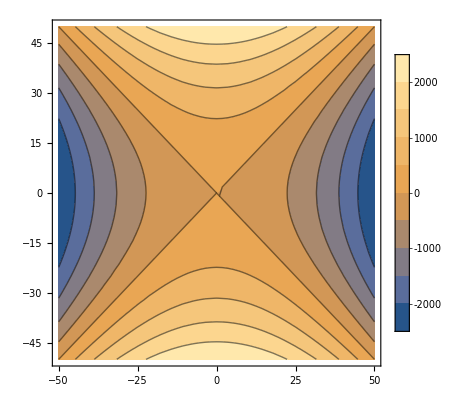

```mathematica
ContourPlot[y^2 - x^2 ,{x,-50,50},{y,-50,50},PlotLegends->Automatic,ScalingFunctions->{"Reverse",None}]
```

```mathematica
(*2. f(x,y)= 2x^2 - 3y^2 + 5z^2*)
(*a. El dominio son todos los R^3, dentro de la elipse con a = 15 y b = 6, hipérbola a lo largo del eje y con asíntotas y = +-2/3 e hipérbola con asíntotas z = +-2/5y.*)
(*b. La imagen son los conjuntos de volúmenes o superficies que satisfacen z = 2x^2 - 3y^2 + 5z^2, para distintos valores de z, en R^3*)
(*C. La imagen de la función es:*)
```

```mathematica
A4 =ContourPlot3D[(2x^2)-(3y^2)+(5*z^2)== 10,{x,-5,5},{y,-5,5},{z,-5,5},ColorFunction->"DarkRainbow"];
A5 =ContourPlot3D[(2x^2)-(3y^2)+(5*z^2)== 20,{x,-5,5},{y,-5,5},{z,-5,5}];
A6=ContourPlot3D[(2x^2)-(3y^2)+(5*z^2)== 30,{x,-5,5},{y,-5,5},{z,-5,5},ColorFunction->Hue];
```

```mathematica
Show[A4,A5,A6]
```

-Graphics3D-

```mathematica
(*d. Mapa de contorno*)
ContourPlot3D[(2x^2)-(3y^2)+(5*z^2),{x,-5,5},{y,-5,5},{z,-5,5},ContourStyle->None]
```

-Graphics3D-

```mathematica
(*e. Mapa de superficies*)
A1 =ContourPlot3D[(2x^2)-(3y^2)+(5*z^2)== 10,{x,-5,5},{y,-5,5},{z,-5,5}, ContourStyle->None];
```

```mathematica
A2 =ContourPlot3D[(2x^2)-(3y^2)+(5*z^2)== 20,{x,-5,5},{y,-5,5},{z,-5,5},ContourStyle->None];
A3 =ContourPlot3D[(2x^2)-(3y^2)+(5*z^2)== 30,{x,-5,5},{y,-5,5},{z,-5,5}, ContourStyle->None];
```

```mathematica
Show[A1,A2,A3]
```

-Graphics3D-